```mathematica
<<Vilcretas`
```

VilCretas está disponible.

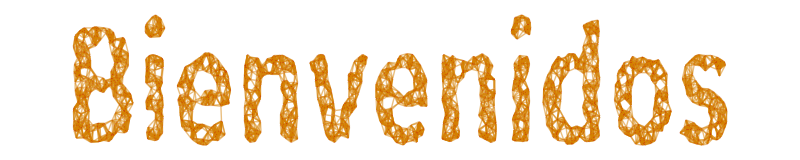

```mathematica
GrafoString["Bienvenidos"]
```

```mathematica
nodos={e,g,a,h,b,f,d,c};
grafo=Grafo[{{a,b},{a,c},{a,d},{a,e},{b,g},{b,h},{c,e},{c,f},{c,g},{d,e},{d,f},{d,g},{d,h},{e,f},{e,g},{e,h},{f,h}},pesos->-{8,4,1,3,10,10,1,4,4,7,6,10,7,1,7,8,3},mostrarpesos->True];
Kruskal[grafo];
```

T={b<->h,b<->g,d<->g,e<->h,a<->b,d<->f,a<->c}

Peso: -56

```mathematica
Prim[grafo,orden->nodos]
```

El orden de los nodos es: {e,g,a,h,b,f,d,c}

T={{e,h},{h,b},{b,g},{g,d},{b,a},{d,f},{g,c}}

Peso: -56

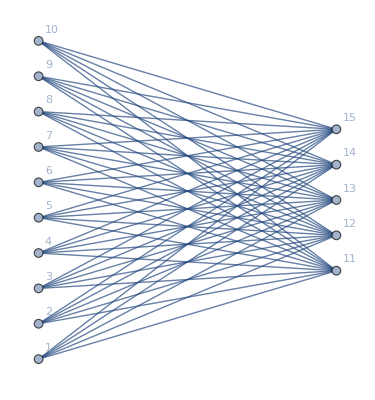

```mathematica
graf=GrafoBipartitoCompleto[10,5]
```

```mathematica
ArbolQ[graf]
```

False

```mathematica
?ArbolQ
```

```mathematica
gr1=Grafo[{{a,f},{a,g},{a,h},{a,j},{b,c},{b,d},{b,e},{b,h},{b,i},{c,e},{d,f},{e,f},{f,g},{f,j},{i,j}},pesos->-{15,3,16,49,32,41,43,3,1,49,25,28,9,11,48},mostrarpesos->True];
```

```mathematica
AlDijkstra[gr1, a,g, all->True]
```

Tabla de pesos del grafo

| a | f | g | h | j | b | c | d | e | i
a | 0 | -15 | -3 | -16 | -49 | 0 | 0 | 0 | 0 | 0
f | -15 | 0 | -9 | 0 | -11 | 0 | 0 | -25 | -28 | 0
g | -3 | -9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
h | -16 | 0 | 0 | 0 | 0 | -3 | 0 | 0 | 0 | 0
j | -49 | -11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -48
b | 0 | 0 | 0 | -3 | 0 | 0 | -32 | -41 | -43 | -1
c | 0 | 0 | 0 | 0 | 0 | -32 | 0 | 0 | -49 | 0
d | 0 | -25 | 0 | 0 | 0 | -41 | 0 | 0 | 0 | 0
e | 0 | -28 | 0 | 0 | 0 | -43 | -49 | 0 | 0 | 0
i | 0 | 0 | 0 | 0 | -48 | -1 | 0 | 0 | 0 | 0

Inicialización: {{a,0,{}},{f,∞,{}},{g,∞,{}},{h,∞,{}},{j,∞,{}},{b,∞,{}},{c,∞,{}},{d,∞,{}},{e,∞,{}},{i,∞,{}}}

Se seleccionó el nodo: a

Lista actual de vértices: {f,g,h,j,b,c,d,e,i}

Lista actual de marcas: {{f,-15,{a}},{g,-3,{a}},{h,-16,{a}},{j,-49,{a}},{b,∞,{}},{c,∞,{}},{d,∞,{}},{e,∞,{}},{i,∞,{}}}

Se seleccionó el nodo: j

Lista actual de vértices: {f,g,h,b,c,d,e,i}

Lista actual de marcas: {{f,-60,{j}},{g,-3,{a}},{h,-16,{a}},{b,∞,{}},{c,∞,{}},{d,∞,{}},{e,∞,{}},{i,-97,{j}}}

Se seleccionó el nodo: i

Lista actual de vértices: {f,g,h,b,c,d,e}

Lista actual de marcas: {{f,-60,{j}},{g,-3,{a}},{h,-16,{a}},{b,-98,{i}},{c,∞,{}},{d,∞,{}},{e,∞,{}}}

Se seleccionó el nodo: b

Lista actual de vértices: {f,g,h,c,d,e}

Lista actual de marcas: {{f,-60,{j}},{g,-3,{a}},{h,-101,{b}},{c,-130,{b}},{d,-139,{b}},{e,-141,{b}}}

Se seleccionó el nodo: e

Lista actual de vértices: {f,g,h,c,d}

Lista actual de marcas: {{f,-169,{e}},{g,-3,{a}},{h,-101,{b}},{c,-190,{e}},{d,-139,{b}}}

Se seleccionó el nodo: c

Lista actual de vértices: {f,g,h,d}

Lista actual de marcas: {{f,-169,{e}},{g,-3,{a}},{h,-101,{b}},{d,-139,{b}}}

Se seleccionó el nodo: f

Lista actual de vértices: {g,h,d}

Lista actual de marcas: {{g,-178,{f}},{h,-101,{b}},{d,-194,{f}}}

Se seleccionó el nodo: d

Lista actual de vértices: {g,h}

Lista actual de marcas: {{g,-178,{f}},{h,-101,{b}}}

Se seleccionó el nodo: g

La longitud de un camino más corto es: -178

Lista actual de vértices: {h}

Lista actual de marcas: {{h,-101,{b}}}

Iteraciones: (a | f | g | h | j | b | c | d | e | i
{0,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}}
{0,{}} | {-15,{a}} | {-3,{a}} | {-16,{a}} | {-49,{a}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}}
{0,{}} | {-60,{j}} | {-3,{a}} | {-16,{a}} | {-49,{a}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {-97,{j}}
{0,{}} | {-60,{j}} | {-3,{a}} | {-16,{a}} | {-49,{a}} | {-98,{i}} | {∞,{}} | {∞,{}} | {∞,{}} | {-97,{j}}
{0,{}} | {-60,{j}} | {-3,{a}} | {-101,{b}} | {-49,{a}} | {-98,{i}} | {-130,{b}} | {-139,{b}} | {-141,{b}} | {-97,{j}}
{0,{}} | {-169,{e}} | {-3,{a}} | {-101,{b}} | {-49,{a}} | {-98,{i}} | {-190,{e}} | {-139,{b}} | {-141,{b}} | {-97,{j}}
{0,{}} | {-169,{e}} | {-3,{a}} | {-101,{b}} | {-49,{a}} | {-98,{i}} | {-190,{e}} | {-139,{b}} | {-141,{b}} | {-97,{j}}
{0,{}} | {-169,{e}} | {-178,{f}} | {-101,{b}} | {-49,{a}} | {-98,{i}} | {-190,{e}} | {-194,{f}} | {-141,{b}} | {-97,{j}}
{0,{}} | {-169,{e}} | {-178,{f}} | {-101,{b}} | {-49,{a}} | {-98,{i}} | {-190,{e}} | {-194,{f}} | {-141,{b}} | {-97,{j}}
{0,{}} | {-169,{e}} | {-178,{f}} | {-101,{b}} | {-49,{a}} | {-98,{i}} | {-190,{e}} | {-194,{f}} | {-141,{b}} | {-97,{j}})

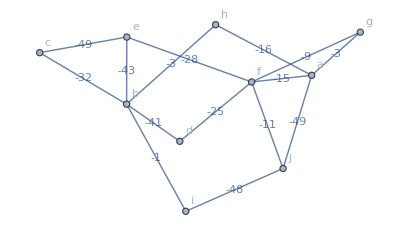

```mathematica
gr1
```

```mathematica
?AlDijkstra
```

```mathematica
?LongitudCaminoMC
```

```mathematica
KnCircuitoEulerQ[21534]
```

False

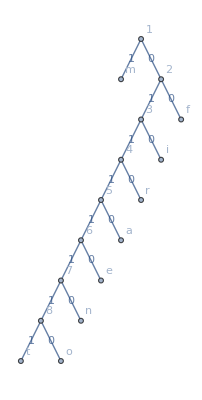

```mathematica
ArbolHuffman["firmamento",optimizado->False,{HileraArbolHuffman["firma", "firmamento", tree->True, optimizado->False]}]
```

```mathematica
HileraArbolHuffman["firma", "firmamento", tree->True, optimizado->False]
```

{000100110101110,-Graphics-}

```mathematica
nodos={d,a,f,g,e,b,c,h};

grafo=Grafo[{{a,b},{a,d},{a,e},{a,f},{b,d},{b,e},{b,g},{b,h},{c,d},{c,f},{c,g},{c,h},{d,e},{e,f},{f,g},{f,h},{g,h}},pesos->{6,9,2,4,2,4,1,9,1,8,2,4,4,3,9,3,2},mostrarpesos->True];

BuscarPrimeroAncho[grafo,orden->nodos]

BuscarPrimeroLargo[grafo,orden->nodos]
```

{{d,a},{d,e},{d,b},{d,c},{a,f},{g,b},{b,h}}

{{d,a},{a,f},{f,g},{g,b},{e,b},{b,h},{c,h}}

```mathematica
Sort/@BuscarPrimeroAncho[grafo,orden->nodos]

Sort/@BuscarPrimeroLargo[grafo,orden->nodos]
```

{{a,d},{d,e},{b,d},{c,d},{a,f},{b,g},{b,h}}

{{a,d},{a,f},{f,g},{b,g},{b,e},{b,h},{c,h}}

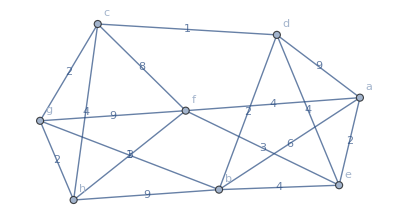

```mathematica
grafo
```